```mathematica
l = 4;
ω0 = {-3,-1,1,3};
β = 0.5;
θ = 0;
Δ = 0.1;
nISI = 80;
snrDB = 8;
ts =1;
npts=1000000;
snr= 10^(snrDB/20);
var=N[Sqrt[(l^2-1)/(6*Log[l,2]*10^(snrDB/10))]];
nsum = 100;
```

(f_X(y) = 1/(√(2π)σ_X)ⅇ^((-(y-ω_0 g_0)^2)/(2 σ_X^2))(1+∑_(m=2)^∞ (α_(2m))/((2m)!σ_X^(2m))H_(2m)((y-ω_0 g_0)/σ_X))
σ_X^2= σ_ν^2+1/3(L^2-1)∑_(k=1)^∞ (g_-k^2+g_k^2)
α_(2m)=κ_(2m)+∑_(i=2)^(m-2) (2m-1
2i)κ_(2(m-i))α_(2i); m ⩾2
κ_m= -j^m T_(m-1) (L^m-1)/(2^m-1)∑_(k=1)^∞ (g_-k^m+g_k^m); m≥2
T_m= d^m/dt^m tan(t)|)_(t=0)
H_prob= H_phys/(2^(m/2)√2 y)

```mathematica
h[1] := 0;
h[-1] := 0;
h[t_]:=(Sinc[(π t)/ts] Cos[(β π t)/ts])/(1-((2 β t)/ts)^2)
g[k_,Δ_]:=g[k]=h[(k+Δ) ts]
hermite[n_,x_,y_]:=HermiteH[n,x]/(√2 2^(n/2)y)
t[m_]:=D[Tan[t],{t,m}]/.t->0
kappa[m_,Δ_]:=N[-(ⅈ^m)*t[m-1]*(l^m-1)/(2^m-1)*Sum[g[-k,Δ]^m + g[k,Δ]^m,{k,1,nsum}]]
```

```mathematica
alpha[0,Δ_] := 1;
alpha[2,Δ_] := 0;
alpha[4,Δ_] := kappa[4,Δ];
alpha[6,Δ_] := kappa[6,Δ];
alpha[tm_,Δ_]:=alpha[tm,Δ] = kappa[tm,Δ]+Sum[Binomial[tm-1,2*i]*kappa[tm-2*i,Δ]*alpha[2*i,Δ],{i,2,(tm/2)-2}]
sigsqr[x_] := 
N[var + 1/3*(l^2-1)*Sum[g[-k,Δ]^2+g[k,Δ]^2,{k,1,nsum}]]
f[x_,y_,w0_,Δ_] := N[1/(√(2π*sigsqr[x]))*Exp[(-(y-w0*g[0,Δ])^2)/(2*sigsqr[x])]*(1+Sum[alpha[2*m]/((2*m)!*sigsqr[x])*hermite[2*m,x,(y-w0*g[0,Δ])/(√sigsqr[x])],{m,2,nsum}])]
```

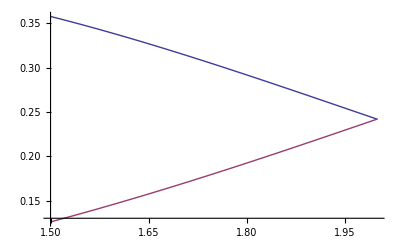

```mathematica
Plot[Evaluate[Table[f[0,y,w,0.01],{w,{1,3}}]],{y,1.5,2}]
```

```mathematica
NSolve[f[0,y,1,0.01]-0.3==0,y]
```

NSolve[-0.3+0.408075 2.71828^(-0.523155 (-0.999812+y)^2) (1.-0.000272318/(-0.999812+y))==0,y]